```mathematica
SetDirectory[NotebookDirectory[]];
Import["FunctionsAndConstants.wl"] ;
Needs["NDSolve`FEM`"];
Needs["NumericalCalculus`"];
Needs["MaTeX`"]
flim=Import["cannex_sensitivity_curves.csv"][[1;;]];
PressSen=Interpolation[flim[[All,1;;2]]]; (*Function of d in meters, output in N/m^2*)
PressGradSen=Interpolation[flim[[All,1;;3;;2]]]; (*Function of d in meters, output in N/m^3*)
```

## Define mesh and plate separation etc here

```mathematica
coordlist[dmin_,ddelta_,dfactor_,nmin_,nmax_]:=Block[{i,dummy},
dummy=Table[N[dmin,5 CPrec],nmax-nmin+1];
If[nmin==0,
For[i=1,i<=nmax,i++,
dummy[[i+1]]=dummy[[i]]+N[ddelta*dfactor^i,5 CPrec];
];,
dummy[[1]]+=Sum[N[ddelta*dfactor^i,5 CPrec],{i,1,nmin}];
For[i=2,i<=nmax-nmin+1,i++,
dummy[[i]]=dummy[[i-1]]+N[ddelta*dfactor^(nmin+i-1),5 CPrec];
];];
N[dummy,5 CPrec]
];
Clear[s,r,z,domb];

Clear[ρV,ρM]

ρV:=2.28274430389522856994287368414079199874719885301117239489836208132800265957484953105449676513671875`1000.*^-20;

rhoV=ρV;

ρM=SetPrecision[2514.0*kgm32MeV4,5 CPrec];

rhoM=ρM;

s=1;

m=m2invMeV;
dd=SetPrecision[10*10^-6,5 CPrec]; (* plate separation in m*)

initialval1[r_,A2_?NumberQ,λ_?NumberQ,β_?NumberQ]:=ϕ2[λ,A2,β,ϕ0[λ,A2,β,ddr/2,ρM,ρV],ddr/2,r,ρM,ρV]


Seed[z_,A2_?NumberQ,λ_?NumberQ,β_?NumberQ]:=initialval1[r[z],A2,λ,β];


Clear[rho];
rho[z_]:=SetPrecision[Piecewise[{{ρV,(-0.5*dd<z<0.5*dd)},{ρM,z≤-0.5*dd||z>=0.5*dd}}],5CPrec];
ρ[z_]:=rho[z]

dist1=SetPrecision[π/(2.0),5CPrec];(* from -∞ to the border of the lower plate*)


(* Was ist dist 2? dp/2 nicht legitim?*)

(*was sollen die kommenden Größen sein?*)
nMaxRes=110*^5;(*max. resolution in the gap 110*^6*)
npts1=80;(*points in free vacuum and free material, 400*)
npts2=80;(*points in the half-gap, 500*)
npts3=80;(*points in the upper plate, 500*)
nFinePoints=30;(*120*)
minMeshSize=SetPrecision[(dd/nMaxRes),5 CPrec];

f1=(*von -π/2 bis -dd/2*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts1-1}],5 CPrec]==SetPrecision[dist1-dd/2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];
(*f2= (*half thickness of the upper plate*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts3-1}],5 CPrec]==SetPrecision[dist2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];*)
(*f3=(*points above upper plate divided by 2*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts1-1}],5 CPrec]==SetPrecision[0.5*(dist1-dp-dd/2)-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];*)
f4=(*half gab between plates*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts2-1}],5 CPrec]==SetPrecision[dd/2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.001},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];

points=SetPrecision[Sort[N[Join[
(* lower plate *)
coordlist[N[-nFinePoints*minMeshSize-dd/2,5 CPrec],-minMeshSize,f1,1,npts1-1],
Table[N[-i*minMeshSize-dd/2,5 CPrec],{i,0,nFinePoints-1}],
Table[N[i*minMeshSize-dd/2,5 CPrec],{i,1,nFinePoints}],
Table[-π/2+N[i*minMeshSize,5 CPrec],{i,1,nFinePoints}] ,
(*in between plates*)
coordlist[N[nFinePoints*minMeshSize-dd/2,5 CPrec],minMeshSize,f4,1,npts2-2],coordlist[dd/2-N[nFinePoints*minMeshSize,5 CPrec],-minMeshSize,f4,1,npts2-1],
Table[dd/2-N[i*minMeshSize,5 CPrec],{i,0,nFinePoints-1}](* inter-spacing *),
Table[dd/2+N[i*minMeshSize,5 CPrec],{i,1,nFinePoints-1}],

(* upper plate *)
coordlist[N[nFinePoints*minMeshSize+dd/2,5 CPrec],minMeshSize,f1,1,npts1-1],
Table[π/2-N[i*minMeshSize,5 CPrec],{i,1,nFinePoints}]

]]](*free space from right*),5CPrec];
points[[1]]=-π/2;
points[[-1]]=π/(2*s);

domb=SetPrecision[ToElementMesh["Coordinates"->Transpose[{points}],"MeshElements"->{LineElement[Table[{i,i+1},{i,1,Length[points]-1}]]},"BoundaryElements"->{(*external boundaries:*)PointElement[{{1},{Length[points]}}]}],5 CPrec];
Length[points]

Clear[b,A]
b[A2_,λ_,β_,ϕOld_,a_,H_]:= Block[{Output},
Output={};
AppendTo[Output,-λ/mpl ⅇ^SetPrecision[(β Log[10]-(λ ϕOld[[1]])/mpl),5 CPrec] -λ^2/mpl^2 ⅇ^SetPrecision[(β Log[10]-(λ ϕOld[[1]])/mpl),5 CPrec]*ϕOld[[1]]+(-a*Block[{$MaxExtraPrecision=1000},ϕρ[A2,λ,β,ρM]])/H[[1]]^2](*From first boundary condition*);
For[i=2, i<=Length[ϕOld]-1,i++, AppendTo[Output, -λ/mpl ⅇ^SetPrecision[(β Log[10]-(λ ϕOld[[i]])/mpl),5 CPrec] -λ^2/mpl^2 ⅇ^SetPrecision[(β Log[10]-(λ ϕOld[[i]])/mpl),5 CPrec]*ϕOld[[i]]]];
AppendTo[Output,-λ/mpl ⅇ^SetPrecision[(β Log[10]-(λ ϕOld[[-1]])/mpl),5 CPrec] -λ^2/mpl^2 ⅇ^SetPrecision[(β Log[10]-(λ ϕOld[[-1]])/mpl),5 CPrec]*ϕOld[[-1]]+(-a*Block[{$MaxExtraPrecision=1000},ϕρ[A2,λ,β,ρM]])/H[[-1]]^2](*from 2nd bountady condition*);
Output]
(*Subscript[ρ, i] computes Subscript[ρ, i] prior to the iterations, such that it is not done repeadedly, same for Subscript[h, i]*)
ρi[points_]:=Block[{Output},
Output={};
For[i=1, i<=Length[points],i++, AppendTo[Output,ρ[points[[i]]]]];
Output]

h[points_]:=Block[{Output},
Output={};
For[i=1, i<=Length[points]-1,i++, AppendTo[Output,(points[[i+1]]-points[[i]])]];
AppendTo[Output,Output[[-1]]]; (*Subscript[h, N] would point outside the degrees of freedom and is therefore not part of points, I just repeat the last entry*);
Output]

(*H refers to the externally computed h, rho to Subscript[ρ, i]*)
A[λ_,A2_,β_,H_,rho_,a_,ϕOld_]:=Block[{Output},
Output=ConstantArray[0,{Length[rho],Length[rho]}](*tridiagonal matrix with mostly 0 elements*); 
Output[[1]][[1]]=-(2a)/H[[1]]^2-λ^2/mpl^2 ⅇ^SetPrecision[(β Log[10]-(λ ϕOld[[1]])/mpl),5 CPrec]-A2/mpl^2 rho[[1]](*from boundary*);
Output[[1]][[2]]=a/H[[1]]^2;

For[i=2, i<=Length[H]-1,i++, 
Output[[i]][[i+1]]=(2a)/(H[[i]](H[[i]]+H[[i-1]]));
Output[[i]][[i-1]]=(2a)/(H[[i-1]](H[[i]]+H[[i-1]]));
Output[[i]][[i]]= -(2a)/(H[[i]](H[[i]]+H[[i-1]]))-(2a)/(H[[i-1]](H[[i]]+H[[i-1]]))-λ^2/mpl^2 ⅇ^SetPrecision[(β Log[10]-(λ ϕOld[[i]])/mpl),5 CPrec]-A2/mpl^2 rho[[i]](*from boundary*)];
Output[[-1]][[-2]]=(2a)/(H[[-2]](H[[-1]]+H[[-2]]));
Output[[-1]][[-1]]=-(2a)/H[[-1]]^2-λ^2/mpl^2 ⅇ^SetPrecision[(β Log[10]-(λ ϕOld[[-1]])/mpl),5 CPrec]-A2/mpl^2 rho[[-1]](*from boundary*);
Output

];

(*The residual function compute the full function for which an N dimensional root is thought, this is the same as the residual error w.r.t. function*)
Residual[λ_,A2_,β_,H_,rho_,a_,ϕOld_]:=Block[{AN,bN,F},
AN=A[λ,A2,β,H,rho,a,ϕOld];
bN=b[A2,λ,β,ϕOld,a,H];
F=AN.ϕOld-bN]


(*This function converts the continous function f into a discrete version that can be used as seed for newtons method*)
CreateSeed[f_,points_]:=Block[{Seed},
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,f[points[[i]]]]];
Seed]

TrivialSeed[points_,λ_,A2_,β_]:=Block[{Seed},
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,Block[{$MaxExtraPrecision=1000},ϕρ[A2,λ,β,ρM]]]];
Seed]

TrivialSeed2[points_,λ_,A2_,β_]:=Block[{Seed,RHO},
RHO=RHO=ρi[points];
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,Block[{$MaxExtraPrecision=1000},ϕρ[A2,λ,β,RHO[[i]]]]]];
Seed]

(*The iterate function takes ϕ^(n-1) and returns ϕ^n*)

Clear[NORM]
NORM[Y1_]:=√Sum[Y1[[i]]^2,{i,Length[points]}]

Iterate[λ_,A2_,β_,H_,rho_,a_,ϕOld_]:=Block[{Output,B2,C2},
B2=b[A2,λ,β,ϕOld,a,H];
C2=A[λ,A2,β,H,rho,a,ϕOld];
Output=LinearSolve[C2,B2];
Output]

(*careful, Seed needs to be converted to a vector prior to using SOLVE*)
SOLVEFD[λ_,A2_,β_,a_,points_,Prec_,Max_,Seed_]:=Block[{YOLD,YNEW,DIFF,M,H,RHO,Func,Output},
M=2;
H=h[points];
RHO=ρi[points];
YOLD=Seed;
YNEW=Iterate[λ,A2,β,H,RHO,a,YOLD];
DIFF=YNEW-YOLD;
While[(NORM[DIFF]/NORM[YOLD]>10^-Prec&&M<=Max),
M=M+1;
YOLD=YNEW;
YNEW=Iterate[λ,A2,β,H,RHO,a,YOLD];
DIFF=YNEW-YOLD;
];
Func={};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],YNEW[[i]]}]];
Output=Interpolation[Func,InterpolationOrder->1];
M=M-1;
(*Print["iterations"M]*);
{YNEW,Output}]
```

494

## Exclusion plot for β = 1

{5.5625,Null}

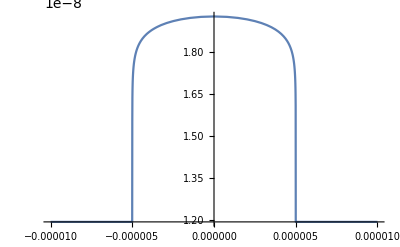

-8.11603657969175741125457673294324660082278823920237263812858099470243449416182881668951745338010604888108491804634848860246136019870158195563215036735004485125823818421306645070902675037161419498398801980582480494916841709796849785311675715182006810276634261689154457393088917397374331242126076022516408415573213295407422299341568927535772204832488657024621546134087016379187726424367043205882169833421546010508015877874878204706683221469292562075709817496916515056046553032592036233907154559973194026485553440705167796622043971256938401239344945583117062989440048059748617165317151288237644140062302582246629561571345345433395126109745739861601533363257346818613836072291101910416755578976031066475969024576729728787068171369040532038914524709367353198727022148558971624322454288250968529872823616115211061383323913987002179738057774930308589061507378095785056934024776195649323838646508308554947057479017925559323032902580628163458174737115477387657479504856482017415741054930033642019789349235769×10^-9

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=30;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=10^31;
A2=10^45;
β=10^0;

Guess=TrivialSeed[points,λ,A2,β];
a=1/m2invMeV^2;
Prec=15;
MAX=100;
Timing[{Vectorform,Solution}=SOLVEFD[λ,A2,β,a,points,Prec,MAX,Guess];]
ϕ0N=Solution[0]; (*This is the numerical value from the simulation ϕ(0)*)

Plot[Solution[z],{z,-dd,dd}]

μm=SetPrecision[10^-6 m2invMeV,1000];
RangeV[λ_,A2_,β_]:=1/μ[A2,λ,β,ρM]/μm
Veff[ϕ_?NumberQ,A_?NumberQ,λ_?NumberQ,β_?NumberQ,ρ_?NumberQ] :=   SetPrecision[ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/(2 mpl^2) ϕ^2,1000]

PressureNum[A2_?NumberQ,λ_?NumberQ,β_?NumberQ,ρV2_?NumberQ,Max_,Prec_]:=If[(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)>0.1,0,
If[RangeV[λ,A2,β]>2.5,0,

ρM/(ρM-ρV2)  (Veff[ϕM[A2,λ,β,ρV],A2,λ,β,ρV2]-Veff[SOLVEFD[λ,A2,β,a,points,Prec,Max,TrivialSeed[points,λ,A2,β]][[2]][0],A2,λ,β,ρV2])* m2invMeV^2/N2invMeV2]]

PressureNum[A2,λ,β,ρV,MAX,Prec]
```

### d = 10 μm

```mathematica
(*Note that originally a 30x30 image was computed here and saved in pressNum, next a finer image was computed in pressNum2 below, using an interpolation of the
original image to speed up calculations. The final result is interpolated here. *)
(*Clear[pressNum,A2,λ,β];
(*<<pressNum2.mx (*imports the list press from above*)
g=Interpolation[pressNum2,InterpolationOrder->1];*)
Prec=15;
MAX=100;
a=1/m2invMeV^2;
β=SetPrecision[1,1000];
pressNum={};
nλ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[16,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[35,5 CPrec];
Amin=SetPrecision[28,5 CPrec];
Amax=SetPrecision[50,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmax-iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum,{λt,At,

PressureNum[A2,λ,β,ρV,MAX,Prec]}]]]],iA]
DumpSave["pressNum.mx",pressNum];*)
```

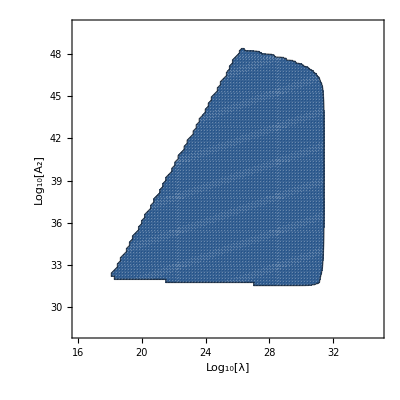

```mathematica
<<pressNum.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
f=Interpolation[pressNum,InterpolationOrder->2];

A=ListContourPlot[pressNum,Contours->{-PressSen[10*^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All]
```

#### Test if upper contour is actually smooth - ok !

```mathematica
(*<<pressNum2.mx (*imports the list press from above*)
g=Interpolation[pressNum2,InterpolationOrder->1];*)
Prec=15;
MAX=100;
a=1/m2invMeV^2;
β=SetPrecision[1,1000];
pressNum2={};
nλ=SetPrecision[30,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[30,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[26,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[28,5 CPrec];
Amin=SetPrecision[47.5,5 CPrec];
Amax=SetPrecision[48.5,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmax-iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum2,{λt,At,

PressureNum[A2,λ,β,ρV,MAX,Prec]}]]]],iA]
DumpSave["pressNum2.mx",pressNum2];
```

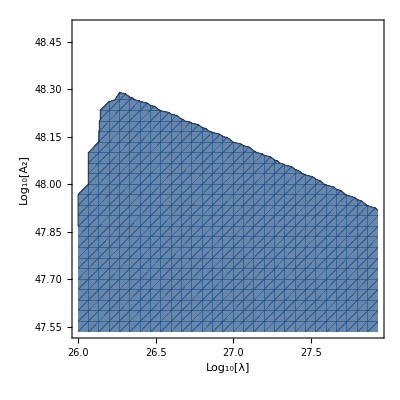

```mathematica
<<pressNum2.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);

F=ListContourPlot[pressNum2,Contours->{-PressSen[10*^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All]
```

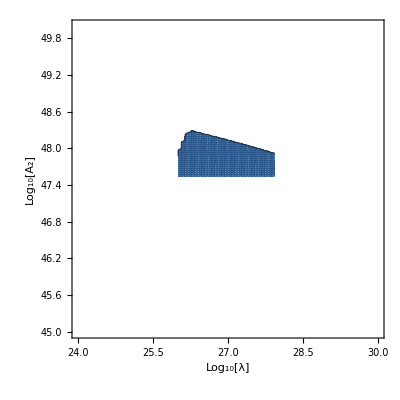

```mathematica
Show[B,PlotRange->{{24,30},{45,50}}]
```

```mathematica
B=ListContourPlot[pressNum2,Contours->{-PressSen[10*^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All]
```

### d = 3 μm

To save computation time, I only compute the pressure for d = 3 μm where it has not been exluded by the case d = 10 μm, since I am only interested in one final plot, including all distance variations. I save 1 if the field was already excluded and 0 else

```mathematica
<<pressNum.mx (*imports the list press from above*)
CHECK={};
For[i=1,i<=Length[pressNum],i++,
If[Abs[pressNum[[i]][[3]]]>Abs[PressSen[10*^-6]],AppendTo[CHECK,{pressNum[[i]][[1]],pressNum[[i]][[2]],1}],AppendTo[CHECK,{pressNum[[i]][[1]],pressNum[[i]][[2]],0}]]]
```

```mathematica
CHECK[[2]]
```

{34.62,28.22,0}

```mathematica
(*Clear[HELP]
HELP=0;
Prec=15;
MAX=100;
a=1/m2invMeV^2;
β=SetPrecision[1,1000];
pressNum3={};
nλ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[16,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[35,5 CPrec];
Amin=SetPrecision[28,5 CPrec];
Amax=SetPrecision[50,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,HELP=HELP+1;
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmax-iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum3,{λt,At,
If[CHECK[[HELP]][[3]]==1, -100,PressureNum[A2,λ,β,ρV,MAX,Prec]]}]]]],iA]
DumpSave["pressNum3.mx",pressNum3];*)
```

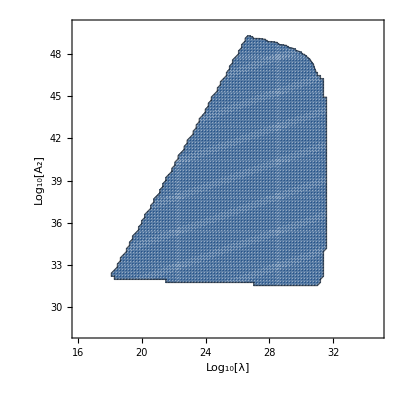

```mathematica
<<pressNum3.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);

B=ListContourPlot[pressNum3,Contours->{-PressSen[3*10^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.5,Y],Opacity[0.01,White]},PlotRange->All]
```

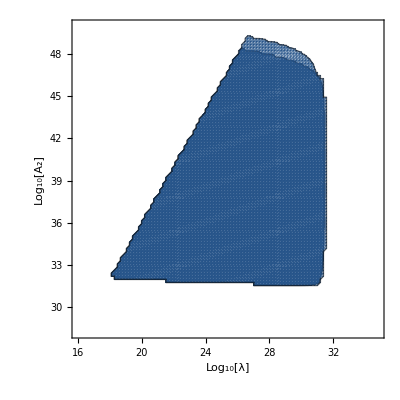

```mathematica
Show[A,B]
```

### d = 30 μm - no improvement over previous cases

```mathematica
(*G=ContourPlot[Abs[f[λ,A2]],{λ,Log10[10^16],Log10[10^32]},{A2,Log10[10^28],Log10[10^50]},FrameLabel->{"Log_10[λ]","Log_10[A_2]"},Contours-> {{0.9}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]*)
```

```mathematica
(*<<pressNum3.mx (*imports the list press from above*)
CHECK={};
For[i=1,i<=Length[pressNum3],i++,
If[Abs[pressNum3[[i]][[3]]]>Abs[PressSen[3*10^-6]],AppendTo[CHECK,{pressNum3[[i]][[1]],pressNum3[[i]][[2]],1}],AppendTo[CHECK,{pressNum3[[i]][[1]],pressNum3[[i]][[2]],0}]]]
f=Interpolation[CHECK, InterpolationOrder->1];

Prec=15;
MAX=100;
a=1/m2invMeV^2;
β=SetPrecision[1,1000];
pressNum4={};
nλ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[16,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[32,5 CPrec];
Amin=SetPrecision[28,5 CPrec];
Amax=SetPrecision[50,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmax-iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum4,{λt,At,
If[f[λt,At]>0.9, -100,PressureNum[A2,λ,β,ρV,MAX,Prec]]}]]]],iA]
DumpSave["pressNum4.mx",pressNum4];*)
```

InterpolatingFunction::dmval: Input value {3/100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

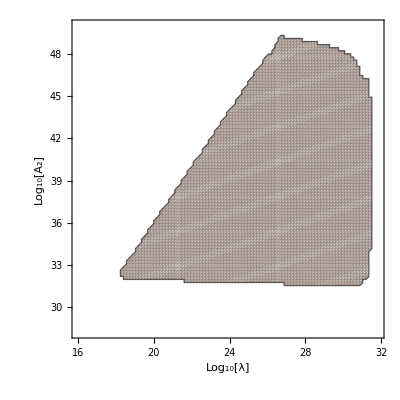

```mathematica
<<pressNum4.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*10/27);

B2=ListContourPlot[pressNum4,Contours->{-PressSen[30*10^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.5,Y],Opacity[0.01,White]},PlotRange->All]
```

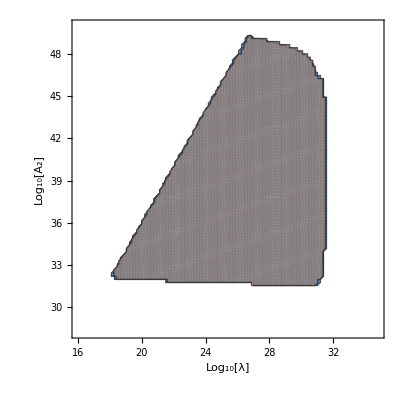

```mathematica
Show[B,B2]
```

### d = 20 μm - no improvement over previous cases

```mathematica
(*Clear[CHECK,f];
<<pressNum4.mx (*imports the list press from above*)
CHECK={};
For[i=1,i<=Length[pressNum4],i++,
If[Abs[pressNum4[[i]][[3]]]>Abs[PressSen[30*10^-6]],AppendTo[CHECK,{pressNum4[[i]][[1]],pressNum4[[i]][[2]],1}],AppendTo[CHECK,{pressNum4[[i]][[1]],pressNum4[[i]][[2]],0}]]]
f=Interpolation[CHECK, InterpolationOrder->1];

Prec=15;
MAX=100;
a=1/m2invMeV^2;
β=SetPrecision[1,1000];
pressNum5={};
nλ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[16,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[32,5 CPrec];
Amin=SetPrecision[28,5 CPrec];
Amax=SetPrecision[50,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmax-iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum5,{λt,At,
If[f[λt,At]>0.9, -100,PressureNum[A2,λ,β,ρV,MAX,Prec]]}]]]],iA]
DumpSave["pressNum5.mx",pressNum5];*)
```

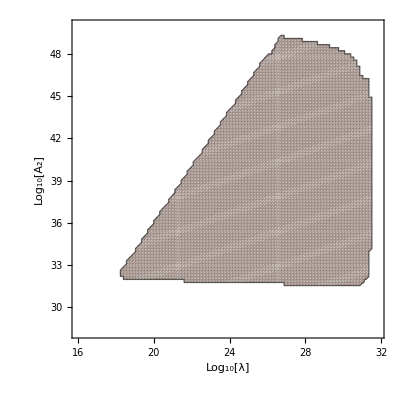

```mathematica
<<pressNum5.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*10/27);

B3=ListContourPlot[pressNum5,Contours->{-PressSen[20*10^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.5,Y],Opacity[0.01,White]},PlotRange->All]
```

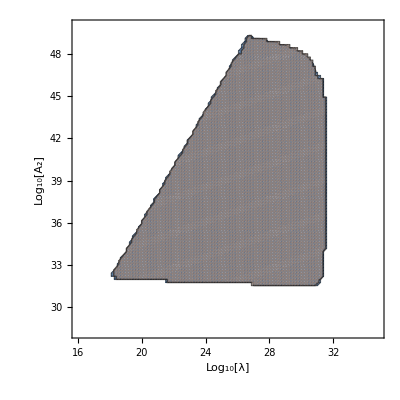

```mathematica
Show[B,B3]
```

### d = 15 μm no improvement over previous cases

```mathematica
(*<<pressNum5.mx (*imports the list press from above*)
CHECK={};
For[i=1,i<=Length[pressNum5],i++,
If[Abs[pressNum5[[i]][[3]]]>Abs[PressSen[20*10^-6]],AppendTo[CHECK,{pressNum5[[i]][[1]],pressNum5[[i]][[2]],1}],AppendTo[CHECK,{pressNum5[[i]][[1]],pressNum5[[i]][[2]],0}]]]
f=Interpolation[CHECK, InterpolationOrder->1];

Prec=15;
MAX=100;
a=1/m2invMeV^2;
β=SetPrecision[1,1000];
pressNum6={};
nλ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[16,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[32,5 CPrec];
Amin=SetPrecision[28,5 CPrec];
Amax=SetPrecision[50,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmax-iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum6,{λt,At,
If[f[λt,At]>0.9, -100,PressureNum[A2,λ,β,ρV,MAX,Prec]]}]]]],iA]
DumpSave["pressNum6.mx",pressNum6];*)
```

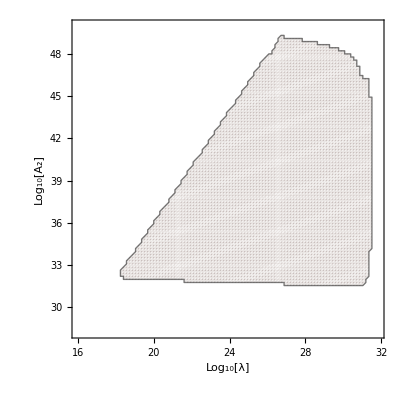

```mathematica
<<pressNum6.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*10/27);

B4=ListContourPlot[pressNum6,Contours->{-PressSen[15*10^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.1,Y],Opacity[0.01,White]},PlotRange->All]
```

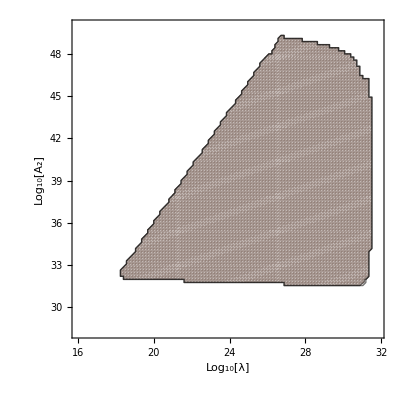

```mathematica
Show[B3,B4]
```

### d = 7 μm

```mathematica
(*<<pressNum.mx (*imports the list press from above*)
CHECK={};
For[i=1,i<=Length[pressNum],i++,
If[Abs[pressNum[[i]][[3]]]>Abs[PressSen[10*^-6]],AppendTo[CHECK,{pressNum[[i]][[1]],pressNum[[i]][[2]],1}],AppendTo[CHECK,{pressNum[[i]][[1]],pressNum[[i]][[2]],0}]]]

Clear[HELP]
HELP=0;
Prec=15;
MAX=100;
a=1/m2invMeV^2;
β=SetPrecision[1,1000];
pressNum7={};
nλ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[16,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[35,5 CPrec];
Amin=SetPrecision[28,5 CPrec];
Amax=SetPrecision[50,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,HELP=HELP+1;
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmax-iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum7,{λt,At,
If[CHECK[[HELP]][[3]]==1, -100,PressureNum[A2,λ,β,ρV,MAX,Prec]]}]]]],iA]
DumpSave["pressNum7.mx",pressNum7];*)
```

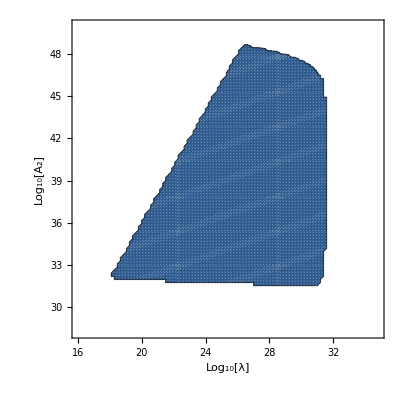

```mathematica
<<pressNum7.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
f=Interpolation[pressNum,InterpolationOrder->2];

B2=ListContourPlot[pressNum7,Contours->{-PressSen[7*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All]
```

```mathematica
Show[A,B,B2]
```

-Graphics-

### d = 5 μm

```mathematica
(*Clear[CHECK,f];
<<pressNum.mx (*imports the list press from above*)
CHECK={};
For[i=1,i<=Length[pressNum],i++,
If[Abs[pressNum[[i]][[3]]]>Abs[PressSen[10*10^-6]],AppendTo[CHECK,{pressNum[[i]][[1]],pressNum[[i]][[2]],1}],AppendTo[CHECK,{pressNum[[i]][[1]],pressNum[[i]][[2]],0}]]]
f=Interpolation[CHECK, InterpolationOrder->1];

Prec=15;
MAX=100;
a=1/m2invMeV^2;
β=SetPrecision[1,1000];
pressNum8={};
nλ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[16,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[32,5 CPrec];
Amin=SetPrecision[28,5 CPrec];
Amax=SetPrecision[50,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmax-iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum8,{λt,At,
If[f[λt,At]>0.9, -100,PressureNum[A2,λ,β,ρV,MAX,Prec]]}]]]],iA]
DumpSave["pressNum8.mx",pressNum8];*)
```

```mathematica
<<pressNum8.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
f=Interpolation[pressNum,InterpolationOrder->2];

B3=ListContourPlot[pressNum8,Contours->{-PressSen[5*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.01,Y],Opacity[0.01,White]},PlotRange->All]
```

-Graphics-

```mathematica
Show[B2,B3]
```

-Graphics-

### d = 12 μm

```mathematica
(*Clear[CHECK,f];
<<pressNum.mx (*imports the list press from above*)
CHECK={};
For[i=1,i<=Length[pressNum],i++,
If[Abs[pressNum[[i]][[3]]]>Abs[PressSen[10*10^-6]],AppendTo[CHECK,{pressNum[[i]][[1]],pressNum[[i]][[2]],1}],AppendTo[CHECK,{pressNum[[i]][[1]],pressNum[[i]][[2]],0}]]]
f=Interpolation[CHECK, InterpolationOrder->1];

Prec=15;
MAX=100;
a=1/m2invMeV^2;
β=SetPrecision[1,1000];
pressNum9={};
nλ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[16,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[32,5 CPrec];
Amin=SetPrecision[28,5 CPrec];
Amax=SetPrecision[50,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmax-iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum9,{λt,At,
If[f[λt,At]>0.9, -100,PressureNum[A2,λ,β,ρV,MAX,Prec]]}]]]],iA]
DumpSave["pressNum9.mx",pressNum9];*)
```

```mathematica
<<pressNum9.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
f=Interpolation[pressNum,InterpolationOrder->2];

B4=ListContourPlot[pressNum9,Contours->{-PressSen[12*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.01,Y],Opacity[0.01,White]},PlotRange->All]
```

-Graphics-

```mathematica
Show[A,B2,B4,B3]
```

-Graphics-

## Exclusion plot β = 10^24

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=30;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=10^31;
A2=10^10;
β=10^24;

Guess=TrivialSeed[points,λ,A2,β];
a=1/m2invMeV^2;
Prec=15;
MAX=100;
Timing[{Vectorform,Solution}=SOLVEFD[λ,A2,β,a,points,Prec,MAX,Guess];]
ϕ0N=Solution[0]; (*This is the numerical value from the simulation ϕ(0)*)

Plot[Solution[z],{z,-dd,dd}]

μm=SetPrecision[10^-6 m2invMeV,1000];
RangeV[λ_,A2_,β_]:=1/μ[A2,λ,β,ρM]/μm
Veff[ϕ_?NumberQ,A_?NumberQ,λ_?NumberQ,β_?NumberQ,ρ_?NumberQ] :=   SetPrecision[ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/(2 mpl^2) ϕ^2,1000]

PressureNum[A2_?NumberQ,λ_?NumberQ,β_?NumberQ,ρV2_?NumberQ,Max_,Prec_]:=If[(A2*ϕM[A2,λ,β,ρV]^2)/(2*mpl^2)>0.1,0,
If[RangeV[λ,A2,β]>2.5,0,

ρM/(ρM-ρV2)  (Veff[ϕM[A2,λ,β,ρV],A2,λ,β,ρV2]-Veff[SOLVEFD[λ,A2,β,a,points,Prec,Max,TrivialSeed[points,λ,A2,β]][[2]][0],A2,λ,β,ρV2])* m2invMeV^2/N2invMeV2]]
PressureNum[A2,λ,β,ρV,MAX,Prec]
```

{0.234375,Null}

-Graphics-

-1.924793264615535962764068313829612191605468559522033921538579649367667812717363844702785778973768746721631712797332672717218195482255009106256785817372510059463955268073271680053661927858076882687063210870886368183734076920897235949181154759651998217980160752900002986096836302980425808961953234299743915472744468573682474023974067281954168711950158388036399382410203352717260183826288490154573872773624656032963256087167590232452679359593011573446957573817138870900303936348883375178542862451483909429814802095106098351023805436018047767356763011576710688255143882823240975953574452512487406971212269636115884112909078019914604705518141444588070299035958408386578752582533634206355619010884884466110253855517942342687582975106874866624032429770925826248458075667192801061933393801755273235063396652585615121411143390641878704110123792589028896505412621485327210801722714289436435322640402204552565059694905881330578734254440975814807727007383189048915625627734336728410594478378016445238×10^-8

```mathematica
A2=10^(SetPrecision[11,100]);
λ=10^(SetPrecision[32,100]);
β=10^24;
Prec=30;
MAX=100;

PressureNum[A2,λ,β,ρV,Prec,MAX]1*^8
```

-0.007291477986962352334823543221915082109767964159395855274349305023257279516446333206100338356070798124066537110974876436432432381937381807681422592740179666944326810504218306042651516331693246568557501314725959900824837261886301266395002203607404783549535861935892394441843669611945733727270719179734907747389475021583697840654037471263970210406476156620835372508343272855290583595922127710609879456788611704816088245612926624893458393323972368295463087447308262212044323425258909417081630843675163032575516654163801490107941339327043063935202164519704764362785735300902981822324619853757294556092881945774246741696852173392730897681447473488673929565282514466514488004725838179531840588500510175997360945919357294319511877385989181559306952716649229427909479645351554311307237399459930975367960847857927679270786227610571130380759447339158822593359294463219813574491591437519098452745902246754410876875735540488741344067218245361301728491716561484127764759903031909054808347764204021012125

### d = 10 μm

```mathematica
(*Clear[pressNum24,A2,λ,β];
Prec=30;
MAX=100;
β=SetPrecision[10^(24),1000];
pressNum24={};
nλ=SetPrecision[30,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[30,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[29,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[31.5,5 CPrec];
Amin=SetPrecision[9,5 CPrec];
Amax=SetPrecision[13.5,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmin+iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum24,{λt,At,

PressureNum[A2,λ,β,ρV,Prec,MAX]}]]]],iA]
DumpSave["pressNum24.mx",pressNum24];*)
```

```mathematica
<<pressNum24.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*24/27);
C2=ListContourPlot[pressNum24,Contours->{-PressSen[10*^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All]
```

-Graphics-

### d = 12 μm

```mathematica
(*Clear[pressNum24B,A2,λ,β];
Prec=30;
MAX=100;
β=SetPrecision[10^(24),1000];
pressNum24B={};
nλ=SetPrecision[30,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[30,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[29,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[31.5,5 CPrec];
Amin=SetPrecision[9,5 CPrec];
Amax=SetPrecision[13.5,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmin+iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum24B,{λt,At,

PressureNum[A2,λ,β,ρV,Prec,MAX]}]]]],iA]
DumpSave["pressNum24B.mx",pressNum24B];*)
```

```mathematica
<<pressNum24B.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*10/27);
C3=ListContourPlot[pressNum24B,Contours->{-PressSen[12*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All]
```

-Graphics-

```mathematica
Show[C2,C3]
```

-Graphics-

### d = 7 μm

```mathematica
(*Clear[pressNum24B2,A2,λ,β];
Prec=30;
MAX=100;
β=SetPrecision[10^(24),1000];
pressNum24B2={};
nλ=SetPrecision[30,5CPrec];  (*Compute that many points in the lambda direction*)
nA=SetPrecision[30,5CPrec]; (*Compute that many points in the A direction*)

λmin=SetPrecision[29,5 CPrec]; (*to be read as λmin=10^20 etc*)
λmax=SetPrecision[31.5,5 CPrec];
Amin=SetPrecision[9,5 CPrec];
Amax=SetPrecision[13.5,5 CPrec];

λIncrement=SetPrecision[(λmax-λmin)/nλ,5CPrec];
AIncrement=SetPrecision[(Amax-Amin)/nA,5CPrec];

Monitor[For[iA=1,iA<=nA,iA++,
For[iλ=1,iλ<=nλ,iλ++,
Block[{A2,λ,At,λt},
At=Amin+iA*AIncrement;
λt=λmin+iλ*λIncrement;
A2=10^At;
λ=10^λt;

AppendTo[pressNum24B2,{λt,At,

PressureNum[A2,λ,β,ρV,Prec,MAX]}]]]],iA]
DumpSave["pressNum24B2.mx",pressNum24B2];*)
```

```mathematica
<<pressNum24B2.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*24/27);
C4=ListContourPlot[pressNum24B2,Contours->{-PressSen[7*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All]
```

-Graphics-

## Total exclusion plot

```mathematica
BACKGROUND=ContourPlot[0,{λ,Log10[10^16],Log10[10^32]},{A2,Log10[10^9],Log10[10^50]},FrameLabel->{"Log_10[λ]","Log_10[A_2]"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.8,Y]},PlotRange->All,PlotTheme->None,WorkingPrecision->100];

<<pressNum.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
A=ListContourPlot[pressNum,Contours->{-PressSen[10*^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All];

<<pressNum3.mx (*imports the list press from above*)

B=ListContourPlot[pressNum3,Contours->{-PressSen[3*10^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.5,Y],Opacity[0.01,White]},PlotRange->All];

<<pressNum7.mx (*imports the list press from above*)

B2=ListContourPlot[pressNum7,Contours->{-PressSen[7*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All];

<<pressNum8.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);

B3=ListContourPlot[pressNum8,Contours->{-PressSen[5*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.01,Y],Opacity[0.01,White]},PlotRange->All];

<<pressNum9.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);

B4=ListContourPlot[pressNum9,Contours->{-PressSen[12*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.01,Y],Opacity[0.01,White]},PlotRange->All];

<<pressNum24.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*24/27);
C2=ListContourPlot[pressNum24,Contours->{-PressSen[10*^-6] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All];

<<pressNum24B.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*10/27);
C3=ListContourPlot[pressNum24B,Contours->{-PressSen[12*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All];

<<pressNum24B2.mx (*imports the list press from above*)
Y=ColorData["M10DefaultDensityGradient"]@(0.8*24/27);
C4=ListContourPlot[pressNum24B2,Contours->{-PressSen[7*10^(-6)] },FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.7,Y],Opacity[0.01,White]},PlotRange->All];
```

```mathematica
CannexFull=Show[BACKGROUND,A,B,B2,B3,B4,C2,C3,C4,PlotRange->{{16,33},{9,50}}]
```

-Graphics-